```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];


Clear[ellipsePhi,ellipseTheta,circle]
circle[x_]={Cos[x],Sin[x]};
ellipsePhi[x_,a_:-Pi/2]={Cos[x-a]/3,Sin[x+a]};
ellipseTheta[x_,a_: 0]={Cos[x+a],Sin[-x-a]/2};
(*Main circle*)
ParametricPlot[circle[x],{x,0,2 Pi},PlotStyle->Black,Epilog->First/@{(*Ellipses*)ParametricPlot[{ellipsePhi[x],ellipsePhi[-x],ellipseTheta[-x],ellipseTheta[x]},{x,0,Pi},PlotStyle->{{Black,Dashed},Black}],(*Co-ordinate axes*)Graphics[Table[GeometricTransformation[{Arrowheads[0.03],Arrow[{{0,0},{1.2,0}}]},ReflectionMatrix[circle[x]]],{x,{Pi/2,-Pi/4,Pi/8}}]],(*mark point,rho,phi& theta directions*)ParametricPlot[{ellipsePhi[x,Pi/2],ellipseTheta[-x,13 Pi/20]},{x,0,Pi/4},PlotStyle->{{Red,Thick},{Blue,Thick}}]/.Line[x__]:>Sequence[Arrowheads[0.03],Arrow[x]],Graphics[{{Directive[Darker@Green,Thick],Arrowheads[0.03],Arrow[{{0,0},ellipsePhi[-3 Pi/4]}]},{Directive[Purple],Disk[ellipsePhi[-3 Pi/4],0.02]}}],(*text*)Graphics[{Text[Style["x",Italic,Larger],1.25 circle[5 Pi/4]],Text[Style["y",Italic,Larger],1.25 circle[0]],Text[Style["z",Italic,Larger],1.25 circle[Pi/2]],Text[Style["ρ",Italic,Larger],0.4 circle[4 Pi/11]],Text[Style["φ",Italic,Larger],1.1 ellipsePhi[Pi+Pi/5]],Text[Style["θ",Italic,Larger],1.1 ellipseTheta[13 Pi/20-Pi/8]],Text[Style["P",Italic,Larger],1.2 ellipsePhi[-3 Pi/4+Pi/24]]}]},Axes->False,PlotRange->1.3 {{-1,1},{-1,1}}]
```

-Graphics-

{Arrow,BoxLine,CarvedArcArrow,CarvedArrow,DashedLine,DiamondLine,DotLine,DottedLine,FilledArcArrow,FilledArrow,HalfFilledArrow,HalfFilledDoubleArrow,HalfUnfilledArrow,HalfUnfilledDoubleArrow,Line,ShortCarvedArcArrow,ShortCarvedArrow,ShortFilledArcArrow,ShortFilledArrow,ShortUnfilledArcArrow,ShortUnfilledArrow,UnfilledArcArrow,UnfilledArrow}

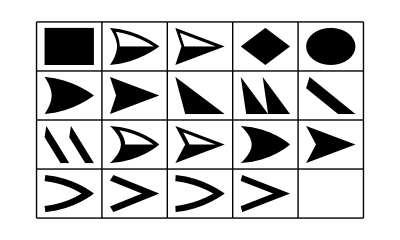

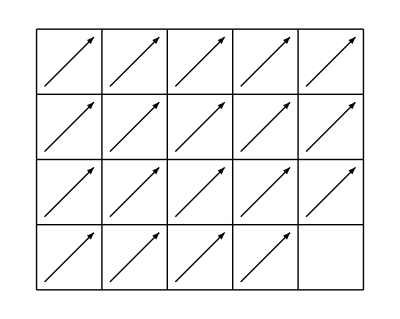

-Graphics3D-

```mathematica
gPrint["Arrow Heads"];
arrowheadNames=GraphElementData["Edge"];
arrowheadNames

headlist=Flatten[Cases[Show[Graph[{1->2},EdgeShapeFunction->#]],Arrowheads[a_]:>Cases[a,_Graphics,Infinity,1],Infinity,1]&/@arrowheadNames];

GraphicsGrid[Partition[headlist,5,5,{1,1},""],Frame->All]

grlist=Graphics[{Arrowheads[{{.3,1,#}}],Arrow[{{0,0},{1,1}}]}]&/@headlist;

GraphicsGrid[Partition[grlist,5,5,{1,1},""],Frame->All]




(*arrow head in 3D*)
myArrowHead=Flatten[Cases[Show[Graph[{1->2},EdgeShapeFunction->"ShortFilledArrow"]],Arrowheads[a_]:>Cases[a,_Graphics,Infinity,1],Infinity,1]][[1]];

Graphics3D[{Arrowheads[{{.1,1,myArrowHead}}],Arrow[{{0,0,0},{1,1,1}}]}]
```